```mathematica
Get[FileNameJoin[{NotebookDirectory[],"QuantumComputing.m"}]]
```

```mathematica
(*This has no evaluation Step*)
```

#### (* Here are the different operators *)

```mathematica
operatorHadamard = QuantumMatrixOperation["Hadamard"];
```

```mathematica
operatorRotate = QuantumMatrixOperation[{"RotZ",Pi/4}];
```

```mathematica
operatorCNOT = QuantumMatrixOperation["CNOT"];
```

```mathematica
operatorPauliZ = QuantumMatrixOperation["SigmaZ"];
```

```mathematica
operatorPauliY = QuantumMatrixOperation["SigmaY"];
```

```mathematica
operatorPauliX = QuantumMatrixOperation["SigmaX"];
```

```mathematica
operatorSqrtNOT = QuantumMatrixOperation[1/2*{{1+I,1-I},{1-I,1+I}}];
```

```mathematica
operatorFourier = QuantumMatrixOperation[{"Fourier",2}];
```

#### (* fixing normalization *)

```mathematica
fixStupidity[expression_]:=((expression)//.{Sqrt[x_]->x,Power[x_,Rational[m_Integer,n_Integer]]->x,Power[x_,Rational[-m_Integer,n_Integer]]->1/x})
```

#### (* generating entanglement tools *)

```mathematica
states = {QuantumFiniteDimensionalState[{{1,0}}],QuantumFiniteDimensionalState[{{0,1}}],QuantumFiniteDimensionalState[{{1,0}}]};
```

```mathematica
generateEntangledState[]:=QuantumFiniteDimensionalState[{"PhiPlus"}]
```

```mathematica
entangledpair = generateEntangledState[]
```

QuantumFiniteDimensionalState[…]

```mathematica
entangledMeasurement = QuantumMeasurement["Observable"-> "SigmaX"];
```

(* create QFDS, of state qubit (j+1) and entangled states *)
(* apply CNOT on state qubit and first entangled qubit *)
(* apply Hadamard on state qubit *)
(* measure state qubit and second entangled qubit *)

```mathematica
entangledThreeState[pair_,states_,j_Integer]:=
QuantumFiniteDimensionalState[fixStupidity[{Normal[states⟦j+1⟧["StateVector"]],Normal[pair["StateVector"]]}]]/;j≠Length[states]

entangledThreeState[pair_,states_,j_Integer]:=
QuantumFiniteDimensionalState[fixStupidity[{Normal[states⟦1⟧["StateVector"]],Normal[pair["StateVector"]]}]]/;j===Length[states]
```

```mathematica
entangledThreeState[entangledpair,states,3];
```

```mathematica
chooseTeleportationOperation[pair_,states_,j_Integer]:=
Flatten[{QuantumEvaluate[{1}-> entangledMeasurement,
QuantumEvaluate[{1}-> operatorHadamard,QuantumEvaluate[{1,2}-> operatorCNOT,entangledThreeState[pair,states,j]]]],QuantumEvaluate[{2}-> entangledMeasurement,QuantumEvaluate[{1,2}-> operatorCNOT,entangledThreeState[pair,states,j]]]
}]
```

```mathematica
chooseTeleportationOperation[generateEntangledState[],states,2]
```

{1,1}

```mathematica
operators = {operatorHadamard,operatorPauliX,operatorPauliY,operatorPauliZ};
```

```mathematica
applyControlOperation[pair_,states_,j_Integer,operators_]:=
Module[{answer=chooseTeleportationOperation[pair,states,j]},
Which[
answer==={-1,-1},
QuantumEvaluate[{1}-> operators⟦1⟧,states⟦j⟧],
answer==={-1,1},
QuantumEvaluate[{1}-> operators⟦2⟧,states⟦j⟧],
answer==={1,-1},
QuantumEvaluate[{1}-> operators⟦3⟧,states⟦j⟧],
answer==={1,1},
QuantumEvaluate[{1}-> operators⟦4⟧,states⟦j⟧]]]
```

```mathematica
applyControlOperation[generateEntangledState[],states,1,operators]
```

QuantumFiniteDimensionalState[…]

(* create new cell based on new control qubit, teleported state qubit, and both of them put through an operator *)

```mathematica
createNewCell[j_Integer,states_,pair_,operators_]:= 
QuantumFiniteDimensionalState[fixStupidity[
{Normal[applyControlOperation[pair,states,j,operators]["StateVector"]]}]]
```

(* repeat for all *)

```mathematica
nextState[pair_,states_,operators_]:= createNewCell[#,states,pair,operators]&/@Range[Length[states]]
```

```mathematica
allStates[pair_,states_,operators_,n_Integer]:= NestList[nextState[pair,#,operators]&,states,n]
```

```mathematica
allStates[generateEntangledState[],states,operators,5];
```

```mathematica
(* in CA, finding disorder and randomness from initial structure is a surprise, in QCA finding order is a surprise? *)
```

#### (*Data Analysis*)

```mathematica
separateStates[states_]:= Map[Normal[#["StateVector"]]&,states]
separateAllStates[states_]:= separateStates[#]&/@states
```

```mathematica
separateAllStates[allStates[generateEntangledState[],states,operators,20]];
```

```mathematica
countEachState[states_]:= Counts[Flatten[separateAllStates[states],1]]
```

```mathematica
showCountEachState[states_]:= BarChart[Sort[countEachState[states]], ChartLabels->Automatic,AxesLabel->Automatic, BarOrigin-> Left, ImageSize->Large]
```

```mathematica
howMuchOfEachState[states_]:= Length[countEachState[states]]
```

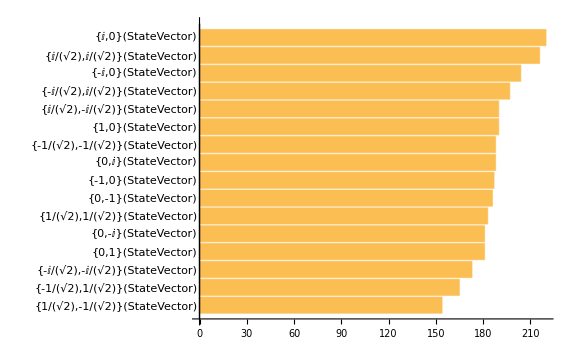

```mathematica
showCountEachState[separateAllStates[allStates[generateEntangledState[],states,operators,1000]]]
```

#### (* Visualization *)

```mathematica
getColour[com_]:= RGBColor[N[Re[com],10],0,N[Im[com],10]]/;Re[com]≥ 0&&Im[com]≥0
getColour[com_]:= Blend[{ColorNegate[RGBColor[Abs[N[Re[com],10]],0,0]],RGBColor[0,0,N[Im[com],10]]}]/;Re[com]≤ 0&&Im[com]≥0
getColour[com_]:= Blend[{RGBColor[Abs[N[Re[com],10]],0,0],ColorNegate[RGBColor[0,0,N[Im[com],10]]]}]/;Re[com]≥ 0&&Im[com]≤0
getColour[com_]:= Blend[{ColorNegate[RGBColor[Abs[N[Re[com],10]],0,0]],ColorNegate[RGBColor[0,0,N[Im[com],10]]]}]/;Re[com]≤ 0&&Im[com]≤0
```

```mathematica
colourQubit[qubit_]:= {getColour[qubit⟦1⟧],getColour[qubit⟦2⟧]}
```

```mathematica
colourQubit[{1,0}]
```

{RGBColor[1., 0, 0],RGBColor[0, 0, 0]}

```mathematica
colourQubit[{0,I}]
```

{RGBColor[0, 0, 0],RGBColor[0, 0, 1.]}

```mathematica
colourQubit[{-1,0}]
```

{RGBColor[0., 0.5, 0.5],RGBColor[0, 0, 0]}

```mathematica
colourQubit[{0,-I}]
```

{RGBColor[0, 0, 0],RGBColor[0.5, 0.5, 0.5]}

```mathematica
colourState[state_]:=Map[colourQubit,state]
```

```mathematica
colourAll[allstates_]:=Map[colourState, allstates]
```

```mathematica
showQubit[qubit_]:= Annotation[Rotate[ArrayPlot[{colourQubit[qubit]},Frame-> False,PlotRangePadding->None, ImageSize->Small],3Pi/2],qubit,"Mouse"]
```

```mathematica
showQubit[{1,0}];
```

```mathematica
showState[state_]:=Map[showQubit,state]
```

```mathematica
showAll[allState_]:= GraphicsGrid[Map[showState,allState],ItemAspectRatio->2]
```

```mathematica
initialState[n_Integer]:=Join[Table[QuantumFiniteDimensionalState[{{1,0}}],(n-1)/2],{QuantumFiniteDimensionalState[{{0,1}}]},Table[QuantumFiniteDimensionalState[{{1,0}}],(n-1)/2]]
```

```mathematica
initialState[5]
```

{QuantumFiniteDimensionalState[…],QuantumFiniteDimensionalState[…],QuantumFiniteDimensionalState[…],QuantumFiniteDimensionalState[…],QuantumFiniteDimensionalState[…]}

```mathematica
ClearAll[QuantumCellularAutomata]
```

```mathematica
QuantumCellularAutomata[operators_,steps_Integer]:= showAll[separateAllStates[allStates[generateEntangledState[],initialState[2*steps + 1],operators,steps]]]
```

```mathematica
QuantumCellularAutomata[operators,50]
```

-Graphics-

```mathematica
QuantumCellularAutomata[operators,10]
```

-Graphics-

```mathematica
Dynamic[MouseAnnotation[]]
```

#### (* Physics Applications *)

```mathematica
onequbit = QuantumFiniteDimensionalState[{{1,0}}];
```

```mathematica
$hbar = 1;
```

```mathematica
$epsilon = 1;
```

```mathematica
$t = 1;
```

```mathematica
matrixHamiltonian1 = {{$epsilon,$t},{$t,-$epsilon}}
```

{{2,1},{1,-2}}

```mathematica
operatorU[t_,hamiltonian_] := QuantumMatrixOperation[N[Cos[hamiltonian*t/$hbar],10]- I*N[Sin[hamiltonian*t/$hbar],10]]
```

```mathematica
operatorU[0, matrixHamiltonian1]
```

QuantumMatrixOperation[…]

```mathematica
qubitEvolve[t_,operator_,initialqubit_,hamiltonian_]:=QuantumFiniteDimensionalState[fixStupidity[{Normal[QuantumEvaluate[{1}-> operator[t,hamiltonian],initialqubit]["StateVector"]]}]]
```

```mathematica
qubitEvolve[0,operatorU,onequbit, matrixHamiltonian1]
```

QuantumFiniteDimensionalState[…]

```mathematica
qubitEvolution[operator_,initialqubit_,hamiltonian_]:=qubitEvolve[#,operator,initialqubit,hamiltonian]&/@Range[0,4*Pi,0.5]
```

```mathematica
qubitEvolution[operatorU,onequbit, $epsilon,$t];
```

```mathematica
showQubitEvolution[operator_,initialqubit_,hamiltonian_]:= GraphicsGrid[{showState[separateStates[qubitEvolution[operator,initialqubit,hamiltonian]]]},ItemAspectRatio->2]
```

```mathematica
showQubitEvolution[operatorU,onequbit, matrixHamiltonian1]
```

-Graphics-

```mathematica
(* increase epsilon and decrease t*)
```

```mathematica
ClearAll[$epsilon,$t,matrixHamiltonian1]
```

```mathematica
(*$t = 0.5;*)
$epsilon= 2;
```

```mathematica
showQubitEvolution[operatorU,onequbit,matrixHamiltonian1]
```

-Graphics-

```mathematica
showQubitEvolution[operatorU,onequbit,matrixHamiltonian1]
```

-Graphics-

```mathematica
Dynamic[MouseAnnotation[]]
```

```mathematica
{showQubitEvolution[operatorU,#,matrixHamiltonian1]}&/@initialState[5]
```

{{-Graphics-},{-Graphics-},{-Graphics-}}

#### Precession

```mathematica
omega = 1;
B = 1;
```

```mathematica
operatorPrecession[t_] := QuantumMatrixOperation[{{N[Cos[omega*t],10]+ I*N[Sin[omega*t]],0},{N[Cos[omega*t],10]- I*N[Sin[omega*t]],0}}]
```

```mathematica
operatorPrecession[1]
```

QuantumMatrixOperation[…]

```mathematica
qubitEvolveP[t_,operator_,initialqubit_]:=QuantumFiniteDimensionalState[fixStupidity[{Normal[QuantumEvaluate[{1}-> operator[t],initialqubit]["StateVector"]]}]]
```

```mathematica
qubitEvolveP[1,operatorPrecession,onequbit]
```

QuantumFiniteDimensionalState[…]

```mathematica
qubitEvolutionP[operator_,initialqubit_]:=qubitEvolveP[#,operator,initialqubit]&/@Range[0,25,0.5]
```

```mathematica
qubitEvolutionP[operatorPrecession,onequbit];
```

```mathematica
showQubitEvolutionP[operator_,initialqubit_]:= GraphicsGrid[{showState[separateStates[qubitEvolutionP[operator,initialqubit]]]},ItemAspectRatio->2]
```

```mathematica
showQubitEvolutionP[operatorPrecession,onequbit]
```

-Graphics-

```mathematica
Dynamic[MouseAnnotation[]]
```

```mathematica
omega = 0.5;
```

```mathematica
showQubitEvolutionP[operatorPrecession,onequbit]
```

-Graphics-

```mathematica
omega = 2;
showQubitEvolutionP[operatorPrecession,onequbit]
```

-Graphics-

#### Coupled 2 Two State Systems

```mathematica
twoqubits = QuantumFiniteDimensionalState[{{1,0},{1,0}}]
```

QuantumFiniteDimensionalState[…]

```mathematica
operatorU2[t_,hamiltonian_]:=QuantumMatrixOperation[N[Cos[hamiltonian*t/$hbar],10]- I*N[Sin[hamiltonian*t/$hbar],10]]
```

```mathematica
qubitEvolve2[t_,operator_,hamiltonian_,initialqubit_]:= QuantumFiniteDimensionalState[fixStupidity[{Normal[QuantumEvaluate[{1,2}-> operator[t,hamiltonian],initialqubit]["StateVector"]]}]]
```

```mathematica
qubitEvolution2[operator_,initialqubit_]:=qubitEvolve2[#,operator,matrixHamiltonian2,initialqubit]&/@Range[0,5,0.5]
```

```mathematica
colourQubit2[qubit_]:= {getColour[qubit⟦1⟧],getColour[qubit⟦2⟧],getColour[qubit⟦3⟧],getColour[qubit⟦4⟧]}
```

```mathematica
colourState2[state_]:=Map[colourQubit2,state]
```

```mathematica
showQubit2[qubit_]:= Annotation[Rotate[ArrayPlot[{colourQubit2[qubit]},Frame-> False,PlotRangePadding->None, ImageSize->Small],3Pi/2],qubit,"Mouse"]
```

```mathematica
showState2[state_]:=Map[showQubit2,state]
```

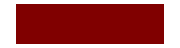
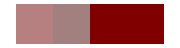
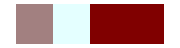
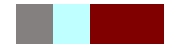
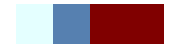
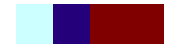
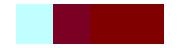
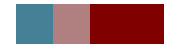

```mathematica
showState2[separateStates[qubitEvolution2[operatorU2,twoqubits]]]
```

```mathematica
showQubitEvolution2[operator_,initialqubit_]:= GraphicsGrid[{showState2[separateStates[qubitEvolution2[operator,initialqubit]]]},ItemAspectRatio->4]
```

```mathematica
showQubitEvolution2[operatorU2,twoqubits]
```

-Graphics-

```mathematica
sigmaX = {{0,1},{1,0}};
sigmaY={{0,-I},{I,0}};
sigmaZ = {{1,0},{0,-1}};
```

#### Heisenberg Spin Chains (NN interactions)

```mathematica
hamiltonianTimeX[t_]:= QuantumMatrixOperation[N[Cos[{{0,1},{1,0}}*t/$hbar]]- I*N[Sin[{{0,1},{1,0}}*t/$hbar]]]
```

```mathematica
hamiltonianTimeY[t_]:= QuantumMatrixOperation[N[Cos[{{0,-I},{I,0}}*t/$hbar]]- I*N[Sin[{{0,-I},{I,0}}*t/$hbar]]]
```

```mathematica
hamiltonianTimeZ[t_]:= QuantumMatrixOperation[N[Cos[{{1,0},{0,-1}}*t/$hbar]]- I*N[Sin[{{1,0},{0,-1}}*t/$hbar]]]
```

```mathematica
nextQubitH[t_,j_Integer,states_]:= Normalize[Normal[QuantumEvaluate[{j}-> hamiltonianTimeX[t],QuantumEvaluate[{j+1}->hamiltonianTimeX[t],states]]["StateVector"]] + Normal[QuantumEvaluate[{j}-> hamiltonianTimeY[t],QuantumEvaluate[{j+1}->hamiltonianTimeY[t],states]]["StateVector"]]+ Normal[QuantumEvaluate[{j}-> hamiltonianTimeZ[t],QuantumEvaluate[{j+1}->hamiltonianTimeZ[t],states]]["StateVector"]]]/;j≠ Log[2,Length[Normal[states["StateVector"]]]]

nextQubitH[t_,j_Integer,states_]:= Normalize[Normal[QuantumEvaluate[{j}-> hamiltonianTimeX[t],QuantumEvaluate[{1}->hamiltonianTimeX[t],states]]["StateVector"]] + Normal[QuantumEvaluate[{j}-> hamiltonianTimeY[t],QuantumEvaluate[{1}->hamiltonianTimeY[t],states]]["StateVector"]]+ Normal[QuantumEvaluate[{j}-> hamiltonianTimeZ[t],QuantumEvaluate[{1}->hamiltonianTimeZ[t],states]]["StateVector"]]]/;j=== Log[2,Length[Normal[states["StateVector"]]]]
```

```mathematica
nextStateH[t_,states_]:= Normalize[Total[nextQubitH[t,#,states]&/@Range[Log[2,Length[Normal[states["StateVector"]]]]]]]
```

```mathematica
fullEvolutionH[states_,timeduration_,timestep_]:= Normal[QuantumFiniteDimensionalState[fixStupidity[{nextStateH[#,states]}]]["StateVector"]]&/@Range[0,timeduration,timestep]
```

```mathematica
evolution=fullEvolutionH[QuantumFiniteDimensionalState[{{1,0},{1,0},{1,0}}],10,0.02];
```

```mathematica
evolution[[1]]
```

{0.612372+0. ⅈ,0.408248+0. ⅈ,0.408248+0. ⅈ,0.204124+0. ⅈ,0.408248+0. ⅈ,0.204124+0. ⅈ,0.204124+0. ⅈ,0.+0. ⅈ}

```mathematica
Norm[#]^2&/@{0.6123724356957946+0. ⅈ,0.4082482904638631+0. ⅈ,0.4082482904638631+0. ⅈ,0.20412414523193154+0. ⅈ,0.4082482904638631+0. ⅈ,0.20412414523193154+0. ⅈ,0.20412414523193154+0. ⅈ,0.+0. ⅈ}
```

```mathematica
norms=Map[Norm[#]^2&,evolution,{2}];
```

```mathematica
Union[Total/@norms]
```

{1.,1.,1.,1.,1.,1.,1.}

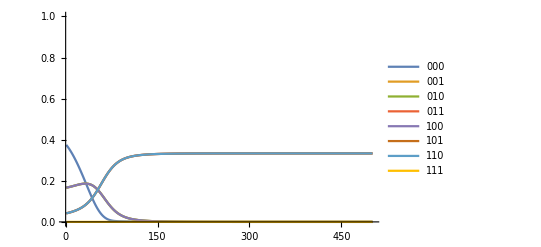

```mathematica
ListLinePlot[Transpose@norms,PlotLegends-> {"000","001","010","011","100","101","110","111"},PlotRange->{0,1}]
```

```mathematica
colourNQubit[qubit_]:= getColour[qubit⟦#⟧]&/@Range[Length[qubit]]
```

```mathematica
showHeisenbergEvolution[states_,timeduration_,timestep_]:= colourNQubit[#]&/@fullEvolutionH[states,timeduration,timestep]
```

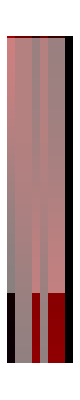

```mathematica
ArrayPlot[showHeisenbergEvolution[QuantumFiniteDimensionalState[{{1,0},{1,0},{1,0}}],2,0.01]]
```

trying to examine smaller systems (two qubits with just xx coupling, just yy ...), create your own iSWAP.
examine sudden jump in QCA, and rotate it, norm grayscale visualization to see populations change. population first phase after. 
measures of entanglement, in between states. Neilson and Isaac Chuang intro to QC. 
for noise : projective measurements.

#### QCA Model, Evolution of Entire State.

matrices is a list of operators, each an operator of airty one.

```mathematica
(*QCA2operators[matrices_]:= matrices⟦#⟧&/@Range[Length[matrices]]*)
```

do the first part for as many things as there are in ^^^ and then add them.

```mathematica
nextQubitQCA2Add[matrices_,j_Integer,states_]:= Normalize[N[Total[Normal[QuantumEvaluate[{j}-> matrices⟦#⟧,QuantumEvaluate[{j+1}-> matrices⟦#⟧,states]]["StateVector"]]&/@Range[Length[matrices]]]]]/;j≠ Log[2,Length[Normal[states["StateVector"]]]]

nextQubitQCA2Add[matrices_,j_Integer,states_]:= Normalize[N[Total[Normal[QuantumEvaluate[{j}-> matrices⟦#⟧,QuantumEvaluate[{1}-> matrices⟦#⟧,states]]["StateVector"]]&/@Range[Length[matrices]]]]]/;j===Log[2,Length[Normal[states["StateVector"]]]]
```

```mathematica
nextStateQCA2Add[matrices_,states_]:= QuantumFiniteDimensionalState[fixStupidity[{Total[nextQubitQCA2Add[matrices,#,states]&/@Range[Log[2,Length[Normal[states["StateVector"]]]]]]}]]
```

```mathematica
nextStateQCA2Add[{operatorHadamard},QuantumFiniteDimensionalState[{{1,0},{1,0},{1,0}}]]
```

QuantumFiniteDimensionalState[…]

```mathematica
evolutionQCA2Add[matrices_, initialstate_,steps_]:= NestList[nextStateQCA2[matrices,#]&,initialstate,steps]
```

```mathematica
evolutionQCA2Add[matrices,QuantumFiniteDimensionalState[{{1,0},{1,0},{1,0}}],10];
```

```mathematica
QuantumCellularAutomata2Add[matrices_,initialstate_,steps_]:= ArrayPlot[colourNQubit[Normal[#["StateVector"]]]&/@evolutionQCA2[matrices,initialstate,steps]]
```

```mathematica
random = QuantumMatrixOperation["RandomUnitary"];
```

```mathematica
matrices = {operatorHadamard};
```

```mathematica
Dynamic[MouseAnnotation[]]
```